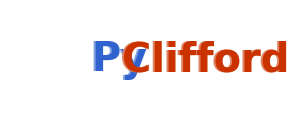

```mathematica
Graphics[{{Opacity[0],Rectangle[{-1,-1},{1,1}]},{Lighter[Blue,0.4],Text[Style["Py",FontSize-> 40,Bold]]},
Translate[{Blue,Text[Style["Py",FontSize-> 40,Bold]]},{0.018,0}],
Translate[{Lighter[Red,0.4],Text[Style["Clifford",FontSize-> 40,Bold]]},{0.95,0}],
Translate[{Red,Text[Style["Clifford",FontSize-> 40,Bold]]},{0.95+0.022,0}],
},ImageSize-> 300,AspectRatio->0.4]
```

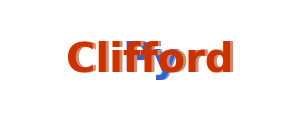

```mathematica
Block[{shadowtext},
shadowtext[txt_,col_,shift_,align_]:={Translate[{Lighter[col,0.4],#},shift],{col,#}}&@Text[Style[txt,FontFamily->"CMU Sans Serif",FontSize-> 40,Bold],{0,0},align];
Graphics[{{Opacity[0],Rectangle[{-1,-1},{1,1}]},{
Translate[shadowtext["Py",Blue,{0.02,0},{1,0}],{0,0}],
Translate[shadowtext["Clifford",Red,{0.02,0},{-1,0}],{0,0}],
}},ImageSize-> 300,AspectRatio->0.4]]
```

```mathematica
Block[{shadowtext},
shadowtext[txt_,col_,shift_,align_]:={Translate[{Lighter[col,0.4],#},shift],{col,#}}&@Text[Style[txt,FontFamily->"Baloo Bhaijaan",FontSize-> 40,Bold],{0,0},align];
Graphics[{{Opacity[0],Rectangle[{-1,-1},{1,1}]},{
Translate[shadowtext["Py",Blue,{0.02,0},{1,0}],{0,0}],
Translate[shadowtext["Clifford",Red,{0.02,0},{-1,0}],{0,0}],
}},ImageSize-> 300,AspectRatio->0.4]]
```

-Graphics-

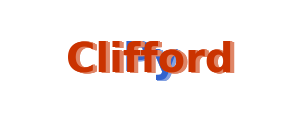

```mathematica
Block[{shadowtext},
shadowtext[txt_,col_,shift_,align_]:={Table[Translate[{Lighter[col,0.4],#},x/10 shift],{x,10,1,-1}],{col,#}}&@Text[Style[txt,FontFamily->"Chalkboard",FontSize-> 40,Bold],{0,0},align];
Graphics[{{Opacity[0],Rectangle[{-1,-1},{1,1}]},{
Translate[shadowtext["Py",Blue,{0.03,-0.03},{1,0}],{0,0}],
Translate[shadowtext["Clifford",Red,{0.03,-0.03},{-1,0}],{0,0}],
}},ImageSize-> 300,AspectRatio->0.4]]
```

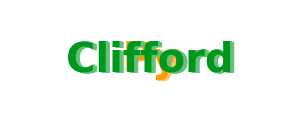

```mathematica
Block[{shadowtext},
shadowtext[txt_,col_,shift_,align_]:={Table[Translate[{Lighter[col,0.4],#},x/10 shift],{x,10,1,-1}],{col,#}}&@Text[Style[txt,FontFamily->"Chalkboard",FontSize-> 40,Bold],{0,0},align];
Graphics[{{Opacity[0],Rectangle[{-1,-1},{1,1}]},{
Translate[shadowtext["Py",Orange,{0.03,-0.03},{1,0}],{0,0}],
Translate[shadowtext["Clifford",Green,{0.03,-0.03},{-1,0}],{0,0}],
}},ImageSize-> 300,AspectRatio->0.4]]
```

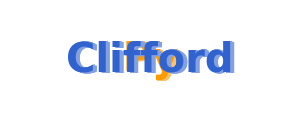

```mathematica
Block[{shadowtext},
shadowtext[txt_,col_,shift_,align_]:={Table[Translate[{Lighter[col,0.4],#},x/10 shift],{x,10,1,-1}],{col,#}}&@Text[Style[txt,FontFamily->"Chalkboard",FontSize-> 40,Bold],{0,0},align];
Graphics[{{Opacity[0],Rectangle[{-1,-1},{1,1}]},{
Translate[shadowtext["Py",Orange,{0.03,-0.03},{1,0}],{0,0}],
Translate[shadowtext["Clifford",Blue,{0.03,-0.03},{-1,0}],{0,0}],
}},ImageSize-> 300,AspectRatio->0.4]]
```

```mathematica
Block[{w=0.3,h=0.3,gate,c,shadowtext},
gate[{i_,j_},l_,col_:Orange]:={EdgeForm[GrayLevel[0.2]],Lighter[col,0.5],
Rectangle[{i-w,l-h},{j+w,l+h},RoundingRadius->0.3h]};
c[r1_,r2_,gap_]:=Block[{cy},
cy[r_]:=Block[{θ0=ArcSin[gap/2/r]},ReIm@Table[r Exp[ⅈ θ],{θ,θ0,2π-θ0,(2π-2θ0)/18}]];
Join[{{(r1+r2)/2,gap/2}},cy[r1],{{(r1+r2)/2,-gap/2}},Reverse@cy[r2]]];
shadowtext[txt_,col_,shift_,align_]:={Table[Translate[{Lighter[col,0.4],#},x/10 shift],{x,10,1,-1}],{col,#}}&@Text[Style[txt,FontFamily->"Chalkboard",FontSize-> 72,Bold],{0,0},align];
Graphics[{Translate[{{GrayLevel[0.2],Translate[Line[{0,#}&/@{0.5,4.5}],{#,0}]&/@Range[6]},{gate[{1,2},1],gate[{4,5},1],gate[{1,3},2],gate[{5,6},2],gate[{1,1},3],gate[{3,3},3],gate[{4,4},3],gate[{6,6},3],gate[{1,3},4],gate[{4,4},4],gate[{6,6},4]}},{-2,-2.5}],
{{{Lighter[Blue,0.5],FilledCurve[#]},{Lighter[Blue,0.],#}}&@BSplineCurve[c[3,5.5,4.5],SplineClosed->True]},
Translate[{{
Translate[shadowtext["Py",Orange,{0.5,-0.5},{1,0}],{0,0}],
Translate[shadowtext["Clifford",Blue,{0.5,-0.5},{-1,0}],{0,0}],
}},{15,0}]},PlotRange->{{-6,42},{-6,6}},ImageSize->{Automatic,120}]]
```

-Graphics-

```mathematica
Block[{w=0.3,h=0.3,gate,c,shadowtext},
gate[{i_,j_},l_,col_:Orange]:={EdgeForm[GrayLevel[0.2]],Lighter[col,0.5],
Rectangle[{i-w,l-h},{j+w,l+h},RoundingRadius->0.3h]};
c[r1_,r2_,gap_]:=Block[{cy},
cy[r_]:=Block[{θ0=ArcSin[gap/2/r]},ReIm@Table[r Exp[ⅈ θ],{θ,θ0,2π-θ0,(2π-2θ0)/18}]];
Join[{{(r1+r2)/2,gap/2}},cy[r1],{{(r1+r2)/2,-gap/2}},Reverse@cy[r2]]];
shadowtext[txt_,col_,shift_,align_]:={Table[Translate[{Lighter[col,0.4],#},x/10 shift],{x,10,1,-1}],{col,#}}&@Text[Style[txt,FontFamily->"Chalkboard",FontSize-> 72,Bold],{0,0},align];
Graphics[{Translate[{{GrayLevel[0.2],Translate[Line[{0,#}&/@{0.5,4.5}],{#,0}]&/@Range[6]},{gate[{1,2},1],gate[{4,5},1],gate[{1,3},2],gate[{5,6},2],gate[{1,1},3],gate[{3,3},3],gate[{4,4},3],gate[{6,6},3],gate[{1,3},4],gate[{4,4},4],gate[{6,6},4]}},{-2,-2.5}],
{{{Lighter[Blue,0.5],FilledCurve[#]},{Lighter[Blue,0.],#}}&@BSplineCurve[c[3,5.5,4.5],SplineClosed->True]}},PlotRange->{{-6,6},{-6,6}},ImageSize->{Automatic,120}]]
```

-Graphics-